# Лабораторная 7. Локальные преобразования и графика

Выполнила студентка ММФ БГУ 
КМ, 1 к, 5 гр. Бельская Е.А.
    27 октября 2019

## Задание 1

Построение первоначального отрезка в пространстве

```mathematica
Fig1=Graphics3D[{AbsoluteThickness[3],Line[{{0,0,0},{1,0,0}}]},Axes->True,AxesLabel->{"X","Y","Z"}];
```

Данный отрезок   и вектор, на который переносится данный отрезок

```mathematica
ab={{0,0,0},{1,0,0}} ;
v={0,1,0};
(#+v)&/@ab
```

{{0,1,0},{1,1,0}}

Координаты нового отрезка

Отрезок и его образ

```mathematica
Fig2=Graphics3D[{{AbsoluteThickness[3],Hue[0],Line[ab]},{AbsoluteThickness[3],Hue[.5],Line[(#+v)&/@ab]}},Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
Fig1//FullForm
```

Graphics3D[List[AbsoluteThickness[3],Line[List[List[0,0,0],List[1,0,0]]]],Rule[Axes,True],Rule[AxesLabel,List["X","Y","Z"]]]

Локальное правило (полуние образов вместе с исходными объектами)

```mathematica
Fig1/.Line[P_]:>{Line[P],Hue[0.3],Line[#+{0,1,0}&/@P]}//FullForm
```

Graphics3D[List[AbsoluteThickness[3],List[Line[List[List[0,0,0],List[1,0,0]]],Hue[0.3],Line[List[List[0,1,0],List[1,1,0]]]]],Rule[Axes,True],Rule[AxesLabel,List["X","Y","Z"]]]

```mathematica
Fig2=Show[Fig1/.Line[P_]:>{Line[P],Hue[.5],Line[#+{0,1,0}&/@P]},Boxed->False,Axes->False]
```

-Graphics3D-

Ассоциация с Fig2 и отображение

```mathematica
ab={{0,0,0},{1,0,0}};
```

```mathematica
v={0,1,0};
```

```mathematica
{#,#+v}&/@ab
```

{{{0,0,0},{0,1,0}},{{1,0,0},{1,1,0}}}

Списки  пар координат концов исходного отрезка и соответстующих концов его образа

```mathematica
Fig2=Show[Fig1/.Line[P_]:>{Line[P],Line[#+v&/@P],Hue[.5],Line[{#,#+v}]&/@P},Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Fig3=Show[Fig2/.Line[P_]:>{Line[P],Line[#+{0,0,1}&/@P],Hue[1/3],Line[{#,#+{0,0,1}}]&/@P},Boxed->False,Axes->False]
```

-Graphics3D-

Клонирование Fig2 по вектору {0, 0, 1}

Функция параллельного переноса

```mathematica
Shift[Fig_,Vector_,Color_]:=Fig/.Line[P_]:>{Line[P],Line[#+Vector&/@P],Color,Line[{#,#+Vector}]&/@P}
```

```mathematica
Show[Fig4=Shift[Fig3,{1.5,1,1},Hue[12]]]
```

-Graphics3D-

```mathematica
Show[Fig5=Shift[Fig4,{-1.5,1,1},Hue[1/6]]]
```

-Graphics3D-

## Задание 2

```mathematica
m={{0,-1},{1,0}}
```

```mathematica
Fract[Fig_]:=Fig/.Line[{A_,B_}]:>{Line[{A,A+(B-A)/4}],Line[{A+(B-A)/4,(m.((B-A)/4))+A+(B-A)/4}],Line[{(m.((B-A)/4))+A+(B-A)/4,(m.((B-A)/4))+A+(B-A)/2}],Line[{(m.((B-A)/4))+A+(B-A)/2,(B-A)/2+A}],Line[{(B-A)/2+A,(m.((A-B)/4))+(B-A)/2+A}],Line[{(m.((A-B)/4))+(B-A)/2+A,(m.((A-B)/4))+3*(B-A)/4+A}],Line[{(m.((A-B)/4))+3*(B-A)/4+A,3*(B-A)/4+A}],Line[{3*(B-A)/4+A,B}]}
```

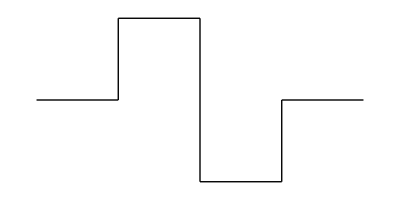

```mathematica
Graphics[Fract[Line[{{2,0},{3,0}}]]]
```

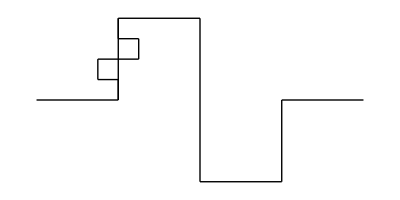

```mathematica
Graphics[{Fract[Line[{{0,0},{1,0}}]],Fract[Line[{{1/4,0},{1/4,1/4}}]]}]
```

```mathematica
Mink[Fig_]:=Fig/.Line[P_]:>{Fract[Line[P]]}
```

```mathematica
Mink[Line[{{0,0},{1,0}}]]
```

{{Line[{{0,0},{1/4,0}}],Line[{{1/4,0},{1/4,1/4}}],Line[{{1/4,1/4},{1/2,1/4}}],Line[{{1/2,1/4},{1/2,0}}],Line[{{1/2,0},{1/2,-1/4}}],Line[{{1/2,-1/4},{3/4,-1/4}}],Line[{{3/4,-1/4},{3/4,0}}],Line[{{3/4,0},{1,0}}]}}

```mathematica
Mink[Fig_,n_]:=Nest[Mink,Fig,n];
```

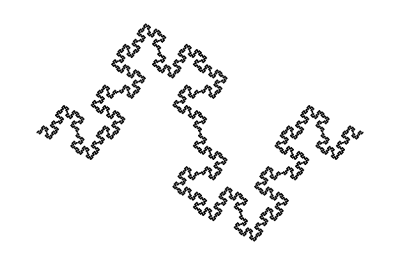

```mathematica
Graphics[Mink[Line[{{0,0},{1,0}}],4]]
```